### Calculate number of photons, electrons and CCD counts for given intensity

```mathematica
params={
QE->0.93, (* camera quantum efficiency *)
μm->Quantity[1 ,"Micrometers"],
lp->Quantity[5 ,"Micrometers"], (* pixel size *)
px->Quantity[13 ,"Micrometers"], (* pixel size *)
h->Quantity[1,"PlanckConstant"],
c->Quantity[1,"SpeedOfLight"],
λ->Quantity[780,"Nanometers"], (* probe laser wavelength *)
μs->Quantity[1,"Microseconds"],
sec ->Quantity[1,"Seconds"],
t->50μs,(* exposure time *)
Δ->0,
I0->0.02,(* factor to express probe intensity in units of saturation intensity *)
Is->Quantity[1.67,("Milliwatts")/("Centimeters")^2],(* saturation intensity *)
na->0.488 (* numerical aperture of Nano objective lens *)
(* , g->1,M->13.128 *)};
```

```mathematica
ρ0=UnitConvert[λ/na,"Micrometers"]/.params (* effective PSF radius *)
σ0=N[UnitConvert[(3 λ^2)/(2π)]]/.params (* atomic scattering cross section *)
```

1.59836 µm

2.9049×10^-13 m^2

```mathematica
γ=UnitConvert[Is/ ((h c)/λ)]/.params (* photon flux at saturation intensity *)
UnitConvert[γ μm^2 μs/.params] (* photons per μm^2 per millisecond at saturation intensity*)
UnitConvert[γ lp^2 μs/.params] (* photons per lattice site per millisecond at saturation intensity*)
UnitConvert[γ px^2 μs/.params] (* photons per pixel per millisecond at saturation intensity*)
UnitConvert[γ π ρ0^2 μs/.params](* probe photons per effective PSF area per millisecond at saturation intensity*)
0.23 UnitConvert[γ π ρ0^2 μs/.params](* signal photons per effective PSF area per millisecond at saturation intensity*)
UnitConvert[γ σ0 μs/.params]
13^2 UnitConvert[γ μm^2 μs/.params]
```

6.55744×10^19 per meter^2per second

65.5744

1639.36

11082.1

526.3

121.049

19.0487

11082.1

Let' s calculate the number of photons per effective PSF area in the scattering signal at 0.02 times the saturation intensity

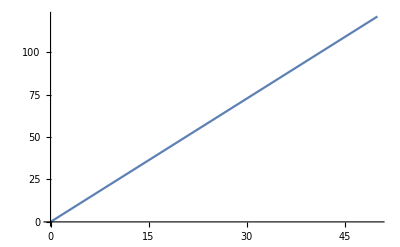

```mathematica
Plot[QuantityMagnitude[UnitConvert[0.23 I0 γ π ρ0^2 μs texp/.params]],{texp,0,50}]
```

The fraction I_abs/I_in in the center (x=0) of the image would be (assuming that the effective area a of the signal is 13×13 μm^2. With π/ρ_0^2=a^-1-> ρ_0=√(π a)).

0.350212

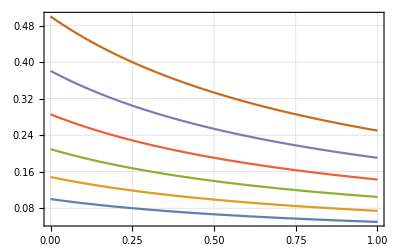

```mathematica
σ0/(1+I0) *π /(λ/na)^2/.params
Plot[Evaluate[Table[ σ0/(1+sp) *π /(λ/Tan[ArcSin[na]])^2/.params,{na,0.25,0.50,0.05}]],{sp,0,1},Frame->True,Axes->False,GridLines->Automatic]
```

```mathematica
Solve[(1.22 780 10^-9)/Tan[ArcSin[na]]==2.5/Sqrt[2] 10^-6,na]
```

{{na→0.473994}}

```mathematica
ρ0=Table[Sqrt[π (n 10^-6)^2],{n,0.9,2.5,0.1}]
```

{1.59521×10^-6,1.77245×10^-6,1.9497×10^-6,2.12694×10^-6,2.30419×10^-6,2.48144×10^-6,2.65868×10^-6,2.83593×10^-6,3.01317×10^-6,3.19042×10^-6,3.36766×10^-6,3.54491×10^-6,3.72215×10^-6,3.8994×10^-6,4.07664×10^-6,4.25389×10^-6,4.43113×10^-6}

```mathematica
navsp0=Table[{na,(QuantityMagnitude[UnitConvert[σ0,("Meters")^2]] *π /((780 10^-9)/Tan[ArcSin[na]])^2),(QuantityMagnitude[UnitConvert[σ0,("Meters")^2]] *π /((780 10^-9)/Tan[ArcSin[na]])^2)/((13 10^-6 Tan[ArcSin[na]])/(1.22 780 10^-9))^2,(13 10^-6 Tan[ArcSin[na]])/(1.22 780 10^-9)},{na,0.25,0.5,0.02}];
navsp0//MatrixForm
```

(0.25 | 0.0976562 | 0.00803736 | 3.52731
0.27 | 0.114724 | 0.00803736 | 3.8308
0.29 | 0.13339 | 0.00803736 | 4.13964
0.31 | 0.153729 | 0.00803736 | 4.45441
0.33 | 0.175827 | 0.00803736 | 4.77573
0.35 | 0.199782 | 0.00803736 | 5.10427
0.37 | 0.225707 | 0.00803736 | 5.44077
0.39 | 0.253729 | 0.00803736 | 5.78604
0.41 | 0.283995 | 0.00803736 | 6.14097
0.43 | 0.316672 | 0.00803736 | 6.50657
0.45 | 0.351955 | 0.00803736 | 6.88392
0.47 | 0.390068 | 0.00803736 | 7.27428
0.49 | 0.431271 | 0.00803736 | 7.67904)

```mathematica
The fraction Subscript[I, abs]/Subscript[I, in] at the center increases with higher NA (second column). However for smaller Airy disks a larger magnification is needed to fill up the pixel with the Airy disk, the higher magnification reduces the intensity in the light signal and absorption signals. As the SNR strongly depends on Subscript[I, in] it is therefore more important to minimize the magnification (Subscript[I, in] scales with the magnifcication SQUARED)
```

```mathematica
((13 10^-6 Tan[ArcSin[0.4]])/(1.22 780 10^-9))^2
```

35.5483

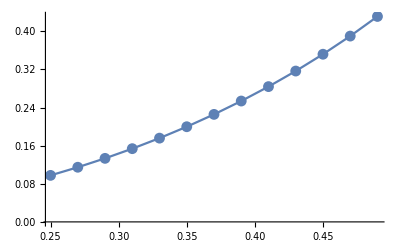

```mathematica
ListLinePlot[navsp0[[All,1;;2]],Mesh->All]
```

```mathematica
u=(3.8317 ρ)/(0.61 Subscript[ρ, 0])
```

(6.28148 ρ)/ρ_0

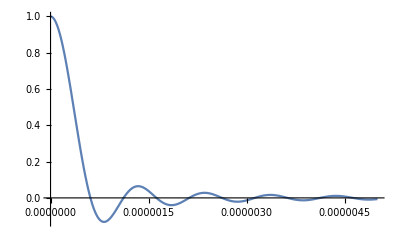

```mathematica
Plot[(2BesselJ[1,u])/u/.Subscript[ρ, 0]->1 10^-6,{ρ,0,5 10^-6},PlotRange->All]
```

```mathematica
Plot[BesselJ[1,√(x^2+y^2)]/(√(x^2+y^2)),{1,6}]
```

Plot[BesselJ[1,√(x^2+y^2)]/(√(x^2+y^2)),{1,6}]

```mathematica
1.26*Sqrt[2]
```

1.78191

```mathematica
l=3.8317(1.26 √2)/2
zero=3.8317
NIntegrate[(2BesselJ[1,(3.8317 √(x^2+y^2))/(0.61 ρ0)])/(√(x^2+y^2)),{x,y}∈Rectangle[{-l/2,-l/2},{l/2,l/2}]]/l^2
NIntegrate[(2BesselJ[1,√(x^2+y^2)])/(√(x^2+y^2)),{x,y}∈Rectangle[{-zero,-zero},{zero,zero}]]/(2 zero)^2
```

3.41387

3.8317

0.782949

0.285051

```mathematica
3.8317/0.61
```

6.28148

Let’s find the optimal fraction by optimizing the central fraction i.c.m. with optimal sampling for a magnification factor of 7.2

```mathematica
na=Sin[ArcTan[d/(2 f)]];
```

```mathematica
r0=(780 10^-9)/Tan[ArcSin[na]];
pr=(r0 BesselJ[1,2  π √(x^2+y^2)/r0])/(π  √(x^2+y^2))
pr2=(2 BesselJ[1,(3.8317 √(x^2+y^2))/(0.61 r0)])/((3.8317 √(x^2+y^2))/(0.61 r0))
lpix={13/7.8 10^-6,13/10.4 10^-6,13/13 10^-6,13/15.04 10^-6,13/5.2 10^-6,13/6.5 10^-6,13 2/15.04 10^-6,13 3/15.04 10^-6}
```

(39 √(1-na^2) BesselJ[1,(100000000 na π √(x^2+y^2))/(39 √(1-na^2))])/(50000000 na π √(x^2+y^2))

(2.48349×10^-7 √(1-na^2) BesselJ[1,(8.05317×10^6 na √(x^2+y^2))/(√(1-na^2))])/(na √(x^2+y^2))

{1.66667×10^-6,1.25×10^-6,1/1000000,8.64362×10^-7,2.5×10^-6,2.×10^-6,1.72872×10^-6,2.59309×10^-6}

```mathematica
Table[r0/.f->40.,{d,{20,30,40}}]
```

{3.12×10^-6,2.08×10^-6,1.56×10^-6}

```mathematica
NIntegrate[pr/.{d->40,f->40},{x,y}∈Rectangle[{-lpix/2,-lpix/2},{lpix/2,lpix/2}]]/lpix^2
```

0.323098

```mathematica
Table[QuantityMagnitude[UnitConvert[σ0,("Meters")^2]] *π /((780 10^-9)/Tan[ArcSin[na]])^2  /.f->40,{d,20,50,4}]
```

{0.09375,0.135,0.18375,0.24,0.30375,0.375,0.45375,0.54}

```mathematica
Table[NIntegrate[pr2/.f->40,{x,y}∈Rectangle[{-#/2,-#/2},{#/2,#/2}]]/#^2,{d,20,50,4}]&/@lpix
```

{{0.789518,0.710805,0.627389,0.542792,0.460274,0.382641,0.31211,0.250224},{0.585026,0.460274,0.346375,0.250224,0.175273,0.121681,0.0869852,0.0670871},{0.710805,0.610455,0.509366,0.412952,0.325564,0.250224,0.188517,0.140665},{0.775385,0.692451,0.605316,0.517858,0.433591,0.355452,0.285654,0.225615}}

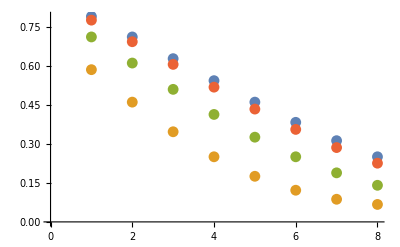

```mathematica
ListPlot[%]
```

```mathematica
naopt=Table[{na,QuantityMagnitude[UnitConvert[σ0,("Meters")^2]] *π /((780 10^-9)/Tan[ArcSin[na]])^2 NIntegrate[pr2,{x,y}∈Rectangle[{-#/2,-#/2},{#/2,#/2}]]/#^2},{na,0.24,0.76,0.02}]&/@lpix;
```

{{{0.24,0.0727649},{0.26,0.0826494},{0.28,0.0924298},{0.3,0.101912},{0.32,0.110896},{0.34,0.119178},{0.36,0.126552},{0.38,0.132821},{0.4,0.137796},{0.42,0.141308},{0.44,0.143217},{0.46,0.143419},{0.48,0.141862},{0.5,0.138559},{0.52,0.1336},{0.54,0.127174},{0.56,0.119576},{0.58,0.111226},{0.6,0.102669},{0.62,0.0945692},{0.64,0.0876884},{0.66,0.0828289},{0.68,0.0807422},{0.7,0.0819868},{0.72,0.0867317},{0.74,0.0945196},{0.76,0.104043}},{{0.24,0.0805386},{0.26,0.0932464},{0.28,0.106516},{0.3,0.120228},{0.32,0.134248},{0.34,0.148425},{0.36,0.162596},{0.38,0.176575},{0.4,0.190163},{0.42,0.203139},{0.44,0.215267},{0.46,0.226293},{0.48,0.235945},{0.5,0.243945},{0.52,0.250006},{0.54,0.253845},{0.56,0.255196},{0.58,0.253827},{0.6,0.249567},{0.62,0.242339},{0.64,0.232204},{0.66,0.21942},{0.68,0.20451},{0.7,0.188342},{0.72,0.1722},{0.74,0.15784},{0.76,0.147456}},{{0.24,0.084395},{0.26,0.0985727},{0.28,0.1137},{0.3,0.12972},{0.32,0.146565},{0.34,0.164158},{0.36,0.182407},{0.38,0.201202},{0.4,0.220418},{0.42,0.239907},{0.44,0.259498},{0.46,0.278992},{0.48,0.298158},{0.5,0.316729},{0.52,0.3344},{0.54,0.35082},{0.56,0.365591},{0.58,0.378268},{0.6,0.388356},{0.62,0.395315},{0.64,0.398573},{0.66,0.397554},{0.68,0.39171},{0.7,0.380603},{0.72,0.364006},{0.74,0.342084},{0.76,0.315641}},{{0.24,0.0861844},{0.26,0.101059},{0.28,0.117075},{0.3,0.134212},{0.32,0.152443},{0.34,0.171732},{0.36,0.192036},{0.38,0.2133},{0.4,0.235456},{0.42,0.258419},{0.44,0.282085},{0.46,0.306326},{0.48,0.330986},{0.5,0.355873},{0.52,0.380756},{0.54,0.405353},{0.56,0.429325},{0.58,0.452263},{0.6,0.473678},{0.62,0.492988},{0.64,0.509505},{0.66,0.522427},{0.68,0.530835},{0.7,0.533701},{0.72,0.529925},{0.74,0.518416},{0.76,0.498254}},{{0.24,0.0542824},{0.26,0.0583189},{0.28,0.0613197},{0.3,0.063167},{0.32,0.0637988},{0.34,0.0632171},{0.36,0.0614934},{0.38,0.0587725},{0.4,0.0552706},{0.42,0.0512694},{0.44,0.0471032},{0.46,0.0431395},{0.48,0.0397513},{0.5,0.0372824},{0.52,0.0360066},{0.54,0.036084},{0.56,0.0375189},{0.58,0.0401284},{0.6,0.0435311},{0.62,0.0471686},{0.64,0.0503718},{0.66,0.0524778},{0.68,0.0529918},{0.7,0.0517643},{0.72,0.0491282},{0.74,0.0459159},{0.76,0.0432897}},{{0.24,0.0656647},{0.26,0.0731479},{0.28,0.0800575},{0.3,0.0861907},{0.32,0.0913579},{0.34,0.0953904},{0.36,0.0981482},{0.38,0.0995296},{0.4,0.0994803},{0.42,0.0980027},{0.44,0.0951657},{0.46,0.0911122},{0.48,0.0860653},{0.5,0.0803303},{0.52,0.0742915},{0.54,0.0684011},{0.56,0.0631571},{0.58,0.0590686},{0.6,0.0566048},{0.62,0.0561273},{0.64,0.0578077},{0.66,0.0615381},{0.68,0.0668516},{0.7,0.072883},{0.72,0.0784158},{0.74,0.0820694},{0.76,0.0826738}},{{0.24,0.0714912},{0.26,0.0809319},{0.28,0.0901744},{0.3,0.0990193},{0.32,0.107263},{0.34,0.114703},{0.36,0.12114},{0.38,0.126387},{0.4,0.130273},{0.42,0.132655},{0.44,0.133426},{0.46,0.132524},{0.48,0.129949},{0.5,0.125773},{0.52,0.120155},{0.54,0.113353},{0.56,0.105733},{0.58,0.0977762},{0.6,0.0900696},{0.62,0.0832889},{0.64,0.078154},{0.66,0.0753571},{0.68,0.0754513},{0.7,0.0786988},{0.72,0.0848842},{0.74,0.0931291},{0.76,0.101781}},{{0.24,0.0521382},{0.26,0.0555878},{0.28,0.0579561},{0.3,0.0591529},{0.32,0.0591509},{0.34,0.0579928},{0.36,0.0557947},{0.38,0.052746},{0.4,0.0491039},{0.42,0.0451819},{0.44,0.0413316},{0.46,0.0379166},{0.48,0.0352802},{0.5,0.033707},{0.52,0.0333814},{0.54,0.0343485},{0.56,0.0364827},{0.58,0.0394743},{0.6,0.0428439},{0.62,0.0459948},{0.64,0.0483084},{0.66,0.0492797},{0.68,0.0486705},{0.7,0.0466399},{0.72,0.0437892},{0.74,0.0410649},{0.76,0.0395004}}}

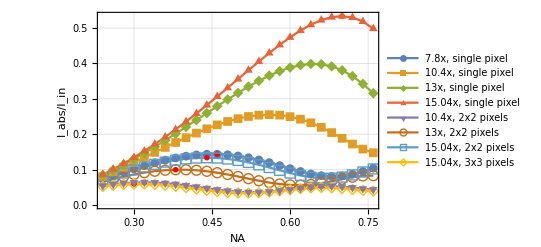

```mathematica
Show[ListPlot[naopt,Joined->True,Mesh->All,PlotMarkers->Automatic,Frame->True,GridLines->Automatic,FrameLabel->{"NA","I_abs/I_in"},LabelStyle->{Medium,Bold},PlotLegends->{"7.8x, single pixel","10.4x, single pixel","13x, single pixel","15.04x, single pixel","10.4x, 2x2 pixels","13x, 2x2 pixels","15.04x, 2x2 pixels","15.04x, 3x3 pixels"}],ListPlot[maxpoints,PlotStyle->Red,PlotMarkers->{Automatic,Medium}]]
```

```mathematica
Export["max_fracs2.pdf",%]
```

max_fracs2.pdf

```mathematica
naopt//MatrixForm
```

((24
0.0959587) | (26
0.106068) | (28
0.115283) | (30
0.123404) | (32
0.13027) | (34
0.135763) | (36
0.139808) | (38
0.142378) | (40
0.14349) | (42
0.143205) | (44
0.14162)
(24
0.062137) | (26
0.0636062) | (28
0.0636465) | (30
0.0623918) | (32
0.0600538) | (34
0.0569015) | (36
0.0532393) | (38
0.0493816) | (40
0.0456305) | (42
0.042254) | (44
0.0394696)
(24
0.0824114) | (26
0.0886687) | (28
0.0935961) | (30
0.097089) | (32
0.0991084) | (34
0.0996799) | (36
0.0988901) | (38
0.0968796) | (40
0.093834) | (42
0.0899732) | (44
0.0855394)
(24
0.0934809) | (26
0.102851) | (28
0.111227) | (30
0.11842) | (32
0.124286) | (34
0.12873) | (36
0.131703) | (38
0.133209) | (40
0.133295) | (42
0.132053) | (44
0.129616)
(24
0.0585348) | (26
0.0592997) | (28
0.0586903) | (30
0.0568882) | (32
0.0541476) | (34
0.0507715) | (36
0.0470848) | (38
0.0434076) | (40
0.0400309) | (42
0.037196) | (44
0.0350794))

```mathematica
Position[naopt,Max[naopt[[1,All,2]]]]
```

{{1,12,2}}

```mathematica
maxs=Table[Position[naopt,Max[naopt[[i,All,2]]]],{i,8}]
```

{{{1,12,2}},{{2,17,2}},{{3,21,2}},{{4,24,2}},{{5,5,2}},{{6,8,2}},{{7,11,2}},{{8,4,2}}}

```mathematica
maxs[[2,1,2]]
```

13

```mathematica
Round[0.099564,0.0001]
```

0.0996

```mathematica
naopt[[1,maxs[[2,1,2]],2]]
```

0.141862

```mathematica
maxpoints=Table[naopt[[maxs[[i,1,1]],maxs[[i,1,2]]]],{i,8}]
```

{{0.46,0.143419},{0.56,0.255196},{0.64,0.398573},{0.7,0.533701},{0.32,0.0637988},{0.38,0.0995296},{0.44,0.133426},{0.3,0.0591529}}

```mathematica
TeXForm[Grid[maxpoints,Frame->All]]
```

```mathematica
\begin{array}{cc}
 0.46 & 0.143419 \\
 0.56 & 0.255196 \\
 0.64 & 0.398573 \\
 0.7 & 0.533701 \\
 0.32 & 0.0637988 \\
 0.38 & 0.0995296 \\
 0.44 & 0.133426 \\
 0.3 & 0.0591529 \\
\end{array}
```

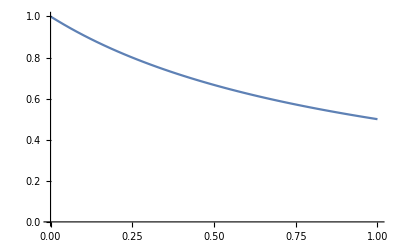

```mathematica
Plot[1/(1+s),{s,0,1},PlotRange->{0,1}]
```

```mathematica
QuantityMagnitude[UnitConvert[σ0,("Meters")^2]] *π /((780 10^-9)/Tan[ArcSin[na]])^2 NIntegrate[pr2/.na->0.3,{x,y}∈Rectangle[{-#/2,-#/2},{#/2,#/2}]]/#^2/.na->0.3&/@{13/15.04 10^-6}
```

{0.134212}

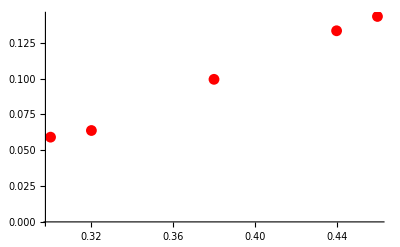

```mathematica
ListPlot[maxpoints,PlotStyle->Red]
```

```mathematica
naopt[[1,9]]
```

{40,0.14349}

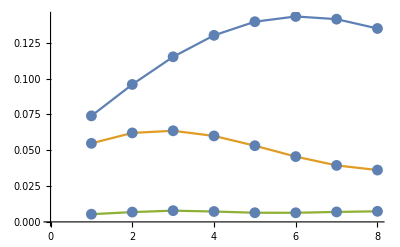

```mathematica
ListPlot[%111,Joined->True,Mesh->All]
```

```mathematica
ListPlot[%1,Joined->True,Mesh->All]
```

-Graphics-

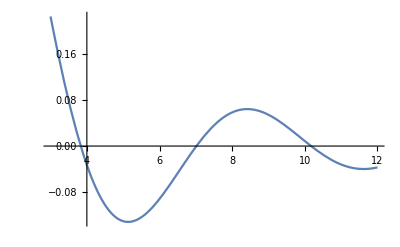

```mathematica
Plot[(2BesselJ[1,zero])/zero,{zero,3,12}]
```

```mathematica
FindRoot[(2BesselJ[1,zero])/zero,{zero,10}]
```

{zero→10.1735}

```mathematica
fr=Table[NIntegrate[(2BesselJ[1,√(x^2+y^2)])/(√(x^2+y^2)),{x,y}∈Disk[{0,0}, zero]]/(π (zero)^2),{rad,{3.8317,3.8317 Sqrt[2],3.8317 2,7.016,10.1735}}]
```

{0.382173,0.382173,0.382173,0.382173,0.382173}

```mathematica
0.38*0.47
```

0.1786

```mathematica
0.09*0.38
```

0.0342

```mathematica
15.04 5/13
```

5.78462

```mathematica
2 13/13
```

2

```mathematica
10.4 40
```

416.

```mathematica
39/(2 10.4)
```

1.875

```mathematica
Limit[(2BesselJ[1,x])/x,x->0]
```

1

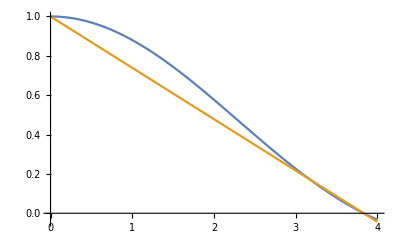

```mathematica
Plot[{(2 BesselJ[1,x])/x,1-x/3.8317},{x,0,4}]
```

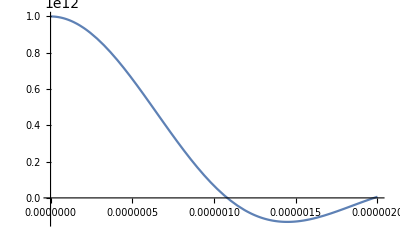

```mathematica
Plot[BesselJ[1,2 π x/ρ0]/(ρ0 x)/.params,{x,0,2 10^-6}]
```

```mathematica
maxlist=Limit[BesselJ[1,2 π x/#]/(# x)&/@ρ0,x->0]
```

{1.23457×10^12,1.×10^12,8.26446×10^11,6.94444×10^11,5.91716×10^11,5.10204×10^11,4.44444×10^11,3.90625×10^11,3.46021×10^11,3.08642×10^11,2.77008×10^11,2.5×10^11,2.26757×10^11,2.06612×10^11,1.89036×10^11,1.73611×10^11,1.6×10^11}

```mathematica
QuantityMagnitude[UnitConvert[σ0,("Meters")^2]]
```

{0.358629,0.29049,0.240074,0.201729,0.171887,0.148209,0.129106,0.113473,0.100515,0.0896573,0.080468,0.0726224,0.0658707,0.0600185,0.054913,0.0504322,0.0464783}

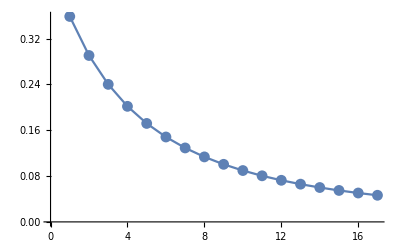

```mathematica
fractions=QuantityMagnitude[UnitConvert[σ0,("Meters")^2]]*maxlist
ListLinePlot[fractions,Mesh->All]
```

```mathematica
% * fr
```

0.111017

Let’s calculate the number of photons in the signal of a single atom in a probe beam with/at saturation intensity.
Here we neglect the term due to the incoherent scattering. Therefore we have I_abs=σ_0/2 I_in.

290490.

```mathematica
sigtab=Table[sigpow[s]=σ0 IntensitySat (s/10)/(1+(s/10)),{s,1,10,2}]
```

{4.41016×10^-10,1.1195×10^-9,1.61706×10^-9,1.99754×10^-9,2.29793×10^-9}

```mathematica
photpersec=UnitConvert[sigtab /(h c/λ)/.params,("Seconds")^-1]
```

{1.7317×10^6,4.39585×10^6,6.34956×10^6,7.84358×10^6,9.02306×10^6}

```mathematica
sig=QuantityMagnitude[photpersec]
```

{1.7317×10^6,4.39585×10^6,6.34956×10^6,7.84358×10^6,9.02306×10^6}

```mathematica
sigtexp=sig texp
```

{1.7317×10^6 texp,4.39585×10^6 texp,6.34956×10^6 texp,7.84358×10^6 texp,9.02306×10^6 texp}

```mathematica
1.7*50
```

85.

We plot a graph of the number of atoms vs the exposure time.

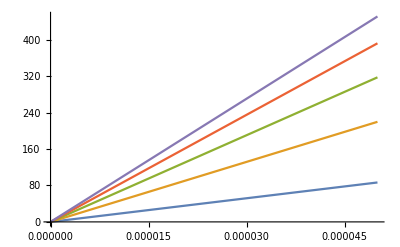

```mathematica
Plot[sigtexp,{texp,0,50 10^-6}]
```

```mathematica
(*pixelsize in object plane px=Subscript[px, ccd]/M*)
(* Gain e-/ADU - from http://www.photomet.com/files/PDF/datasheets/es2.pdf*)
(* Electronic signal per pixel, gain (electrons/count),QE=electrons/photon,M=Magnification of imaging system *)
```

```mathematica
IntensitySat=Quantity[1.67,("Milliwatts")/("Centimeters")^2];
Intensity=I0 IntensitySat;
PhotonNumber=t Intensity px^2 λ/(h c);
detPhotonNumber=(1.36)PhotonNumber;
ADU=QE/g PhotonNumber;
detADU=QE/g detPhotonNumber;

Nph=UnitConvert[PhotonNumber/.params,1] ;
Print["N_ph=",Nph]
Ne=UnitConvert[ADU g/.params,1];
Print["N_e=",Ne]
Nadu=UnitConvert[ADU/.params,1];
Print["N_adu=",Nadu]
Ndet=UnitConvert[detPhotonNumber/.params,1] 
Ndetadu=UnitConvert[detADU/.params,1] 


Noise2=√2(QE PhotonNumber)^(-1/2)/.params  (*√2 from division of two noisy images, electron noise and photon noise add in quadrature *)
Δpx=UnitConvert[Noise/.params,1];
Print["Δ_px=",Δpx]
```

N_ph=64.3019

$Aborted

N_e=Ne

$Aborted

N_adu=Nadu

$Aborted

$Aborted

0.182878

Δ_px=UnitConvert[Noise,1]

```mathematica
1
```

1

```mathematica
Noise=Ndetadu/Nadu^2+(Ndetadu^2 Nadu)/Nadu^4
```

0.0536715

```mathematica
PhotonNumber/.params
```

64.3019

### Expected signal (absorption)

```mathematica
σ0=(3. λ^2)/(2π)/.params
n2d=Quantity[1,("Micrometers")^-2];
σ=σ0/(1.+Intensity/IntensitySat+4 Δ^2)/.params
(*Signal=UnitConvert[1-Exp[-σ n2d]/.params,1]*)
Signal=1.36
```

290490.

284794.

1.36

25.3393

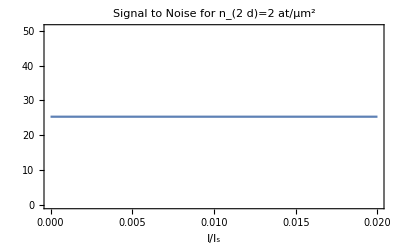

```mathematica
SNR=UnitConvert[Signal/Noise/.params,1]
Plot[SNR(*,5(1+Tanh[100 (I1-1)])}*),{I1,0,0.02},PlotRange->Automatic,Frame->True,PlotLabel->"Signal to Noise for n_(2  d)=2 at/μm^2",FrameLabel->"I/I_s"]
```

Optimal signal to noise achieved for I/Is between 1 and 2, depending on atomic density.

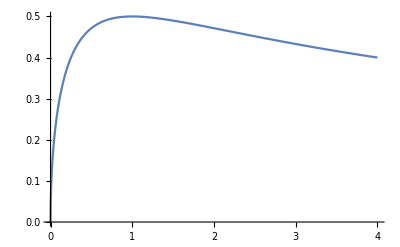

```mathematica
Plot[(√s)/(1+s),{s,0,4},PlotRange->{0,All}]
```

```mathematica
noise[s_]:=(nabs/nref)/Sqrt[(ndet/nref^2+(ndet^2 nref)/nref^4)]
```

nabs/(√(ndet^2/nref^3+ndet/nref^2) nref)

```mathematica
ndet=(1-fr)nref;
nabs=nref-ndet
```

nref-(1-fr) nref

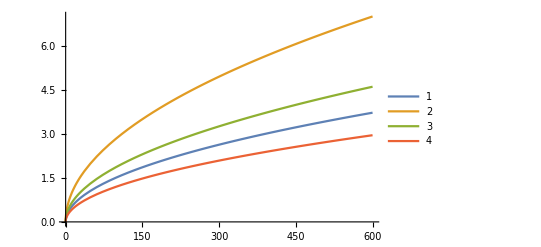

```mathematica
Plot[Evaluate[{noise/.{fr->0.15/(1+#),nref->2x},noise/.{fr->0.34/(1+#),nref->x },noise/.{fr->0.133/(1+#),nref->4x},noise/.{fr->0.06/(1+#),nref->9x}}&/@{0.1}],{x,0,600},PlotLegends->Automatic]
```

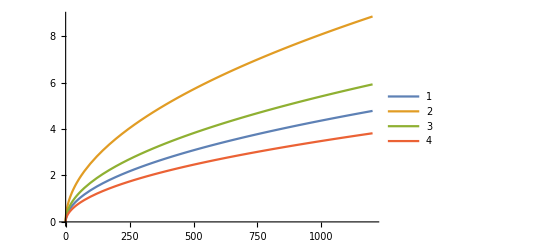

```mathematica
Plot[Evaluate[{noise/.{fr->0.15/(1+#),nref->2x},noise/.{fr->0.34/(1+#),nref->x },noise/.{fr->0.133/(1+#),nref->4x},noise/.{fr->0.06/(1+#),nref->9x}}&/@{0.2}],{x,0,1200},PlotLegends->Automatic]
```

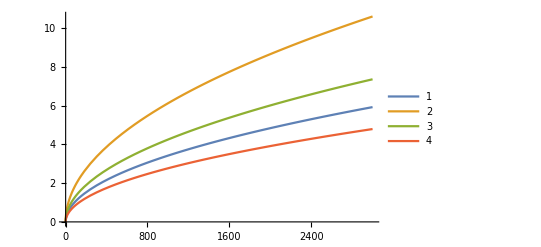

```mathematica
Plot[Evaluate[{noise/.{fr->0.15/(1+#),nref->2x },noise/.{fr->0.34/(1+#),nref->x},noise/.{fr->0.133/(1+#),nref->4x },noise/.{fr->0.06/(1+#),nref->9x }}&/@{0.5}],{x,0,3000},PlotLegends->Automatic]
```

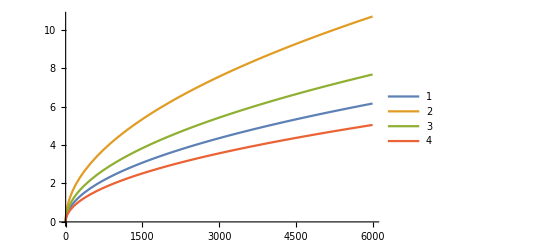

```mathematica
Plot[Evaluate[{noise/.{fr->0.15/(1+#),nref->2x#},noise/.{fr->0.34/(1+#),nref->x #},noise/.{fr->0.133/(1+#),nref->4x #},noise/.{fr->0.06/(1+#),nref->9x #}}&/@{1}],{x,0,6000},PlotLegends->Automatic]
```

```mathematica
ndet=x/1.36
nxdet=xdet/1.36
xdet=(1-0.17)x
```

x

0.57 x

0.83 x

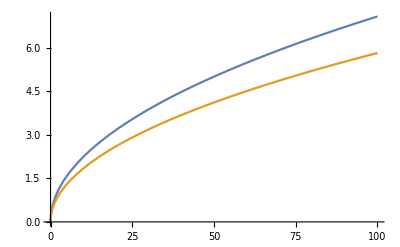

```mathematica
Plot[{(ndet/x)/Sqrt[ndet/x^2+(ndet^2 x)/x^4],(nxdet/xdet)/Sqrt[nxdet/xdet^2+(nxdet^2 xdet)/xdet^4]},{x,0,100}]
```

```mathematica
nxdet/xdet^2+(nxdet^2 xdet)/xdet^4/(nxdet/xdet)^2
```

1.86591/x

```mathematica
Sqrt[1.866/50]
```

0.193184

```mathematica
1.2*1.36/1.36^2
```

0.882353

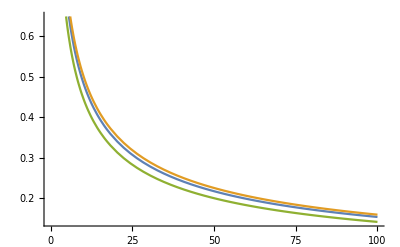

```mathematica
Plot[{Sqrt[ndet/x^2+(ndet^2 x)/x^4]*1.36,Sqrt[nxdet/xdet^2+(nxdet^2 xdet)/xdet^4]*1.36,Sqrt[2/x]},{x,0,100}]
```

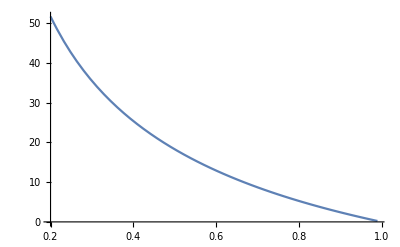

```mathematica
nabs=natt-nref;
natt=x nref;
Plot[(1-natt/nref)/(√(natt/nref^2+(natt^2 nref)/nref^4))/.nref->1000,{x,0.2,0.99}]
```

```mathematica
FullSimplify[(1-natt/nref)/(√(natt/nref^2+(natt^2 nref)/nref^4))]
```

(1-x)/(√((x (1+x))/nref))

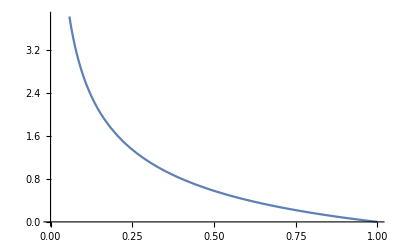

```mathematica
Plot[(1-x)/√(x(1+x)),{x,0,1}]
```

```mathematica
Solve[(1-x)/(√(x(1+x)))==1,x]
```

{{x→1/3}}

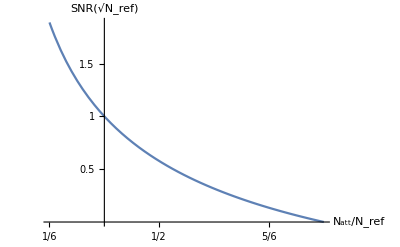

```mathematica
Plot[(1-x)/(√(x(1+x))),{x,1/6,1},AxesOrigin->{1/3,0},Ticks->{{1/6,2/6,3/6,4/6,5/6,1},{0.5,1,1.5}},AxesLabel->{"N_att/N_ref","SNR(√N_ref)"},LabelStyle->Directive[Black,Bold]]
```

```mathematica
Export["snr.pdf",Plot[(1-x)/(√(x(1+x))),{x,1/6,1},AxesOrigin->{1/3,0},Ticks->{{1/6,2/6,3/6,4/6,5/6,1},{0.5,1,1.5}},AxesLabel->{"N_att/N_ref","SNR(√N_ref)"},LabelStyle->Directive[Black,Bold]]]
```

snr.pdf

```mathematica
(1-x)/(√(x(1+x)))/.x->0.2
```

1.63299

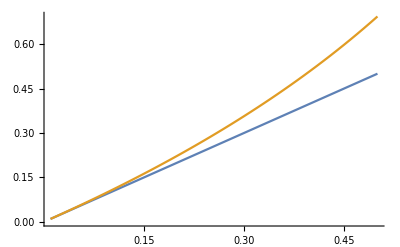

```mathematica
Plot[{nabs/nref/.nref->100,-Log[ndet/nref]/.nref->1000},{fr,0.01,0.5}]
```